# How to Optimally Cut An Onion: A Love Letter to the Jacobian

For each section in the paper, we provide Mathematica code that verifies the solutions presented.

## Inspiration for the Solution

Jacobian for the h=0 case

```mathematica
x[r_,θ_]:=r Cos[θ];
y[r_,θ_]:= r Sin[θ];
J[r_,θ_]:=Abs[D[x[r,θ],r]D[y[r,θ],θ]-D[x[r,θ],θ]D[y[r,θ],r]]
```

```mathematica
FullSimplify[Abs[J[r,θ]]]
```

Abs[r]

Onion cutting statistics in the h=0 case

```mathematica
Abar=Assuming[R>0,Integrate[J[r,θ],{r,0,R},{θ,0,Pi/2}]/Integrate[1,{r,0,R},{θ,0,Pi/2}]]
```

R/2

```mathematica
σ2=Assuming[R>0,Integrate[(J[r,θ]-Abar)^2,{r,0,R},{θ,0,Pi/2}]/Integrate[1,{r,0,R},{θ,0,Pi/2}]]
```

R^2/12

```mathematica
Abar=Assuming[R>0,Integrate[r/R,{r,0,R},{θ,0,Pi/2}]/Integrate[1/R,{r,0,R},{θ,0,Pi/2}]]
```

R/2

```mathematica
σ2=Assuming[R>0,Integrate[(r/R-Abar)^2,{r,0,R},{θ,0,Pi/2}]/Integrate[1/R,{r,0,R},{θ,0,Pi/2}]]
```

(2 ((π R)/6-(π R^2)/4+(π R^3)/8))/π

Compare to the uniform distribution:

```mathematica
Mean[UniformDistribution[{0,R}]]
```

R/2

```mathematica
Variance[UniformDistribution[{0,R}]]
```

R^2/12

## A Strange Coordinate System

c_h, x_h, y_h, and J_h from the paper:

```mathematica
ch[r_,θ_,h_]:=h Cos[θ]+Sqrt[r^2-h^2 Sin[θ]^2];
xh[r_,θ_,h_]:=ch[r,θ,h] Sin[θ];
yh[r_,θ_,h_]:= ch[r,θ,h] Cos[θ]-h;
Jh[r_,θ_,h_]:=D[xh[r,θ,h],r]D[yh[r,θ,h],θ]-D[xh[r,θ,h],θ]D[yh[r,θ,h],r]
```

```mathematica
cm[r_,θ_,h_]:=h Cos[θ]-Sqrt[r^2-h^2 Sin[θ]^2];
```

Note that the absolute value of the Jacobian is the below expression with the absolute value removed, since r>h tan(θ) and tan(θ)>sin(θ) on this interval. Moreover, r>0,h>0 and cos(θ)>0.

```mathematica
FullSimplify[Jh[r,θ,h]]
```

r (-1-(h Cos[θ])/(√(r^2-h^2 Sin[θ]^2)))

So, let’s redefine Jh to be positive:

```mathematica
Jh[r_,θ_,h_]:=r+(h r Cos[θ])/(√(r^2-h^2 Sin[θ]^2))
```

## Calculating Statistics

The next two calculations are for the denominator of Abar(h) in the paper. We do the inner integral, then the outer.

```mathematica
Integrate[1,{r,h Tan[θ],1}]
```

1-h Tan[θ]

```mathematica
Assuming[h>0,Integrate[1-h Tan[θ],{θ,0,ArcTan[1/h]}]]
```

ArcTan[1/h]-1/2 h Log[1+1/h^2]

This allows us to define Abar(h)

```mathematica
Abarh[h_]=Pi/(4(ArcTan[1/h]-1/2 h Log[1+1/h^2]))
```

π/(4 (ArcTan[1/h]-1/2 h Log[1+1/h^2]))

This next code calculates the integrand of f(h) in the paper, when we change coordinates from the onion coordinate system to rectangular coordinates

```mathematica
Clear[x,y]
```

```mathematica
Assuming[x>0&&y>0&&h>0,FullSimplify[Jh[Sqrt[x^2+y^2],ArcTan[x/(y+h)],h]]]
```

(√(x^2+y^2) (x^2+(h+y)^2))/(x^2+y (h+y))

```mathematica
integrand[x_,y_,h_]:=(√(x^2+y^2) (x^2+(h+y)^2))/(x^2+y (h+y))
```

```mathematica
Assuming[s>0,FullSimplify[integrand[s Cos[ϕ],s Sin[ϕ],h]]]
```

(h^2+s^2+2 h s Sin[ϕ])/(s+h Sin[ϕ])

Finally, we calculate f(h) by performing the double integral in polar coordinates from the paper

```mathematica
Assuming[0<h<1,(∫_0^1 ∫_0^(π/2) ((h^2+s^2+2 h s Sin[ϕ])/(s+h Sin[ϕ]))sⅆϕⅆs)]
```

1/6 (h+2 π+4 (1-h^2)^(3/2) ArcSin[h]-4 (1-h^2)^(3/2) ArcTan[(1+h)/(√(1-h^2))]+h^3 Log[4 h^2])

so, we can define f(h)

```mathematica
f[h_]=1/6 (h+2 π+4 (1-h^2)^(3/2) ArcSin[h]-4 (1-h^2)^(3/2) ArcTan[(1+h)/(√(1-h^2))]+h^3 Log[4 h^2]);
```

So, by the formula for σ^2(h) in the paper,

```mathematica
σ2h[h_]=f[h]/(ArcTan[1/h]-1/2 h Log[1+1/h^2])-Abarh[h]^2
```

-π^2/(16 (ArcTan[1/h]-1/2 h Log[1+1/h^2])^2)+(h+2 π+4 (1-h^2)^(3/2) ArcSin[h]-4 (1-h^2)^(3/2) ArcTan[(1+h)/(√(1-h^2))]+h^3 Log[4 h^2])/(6 (ArcTan[1/h]-1/2 h Log[1+1/h^2]))

And, making different assumptions, we can calculate the limit as h->infinity:

```mathematica
Assuming[h>1,(∫_0^1 ∫_0^(π/2) ((h^2+s^2+2 h s Sin[ϕ])/(s+h Sin[ϕ]))sⅆϕⅆs)]
```

1/6 (h+2 π+2 h^3 Log[2 h]-2 √(-1+h^2) ((1+2 h^2) Log[h-√(-1+h^2)]+3 h^2 Log[h+√(-1+h^2)]))

```mathematica
f[h_]=1/6 (h+2 π+2 h^3 Log[2 h]-2 √(-1+h^2) ((1+2 h^2) Log[h-√(-1+h^2)]+3 h^2 Log[h+√(-1+h^2)]));
```

```mathematica
σ2h[h_]=f[h]/(ArcTan[1/h]-1/2 h Log[1+1/h^2])-Abarh[h]^2
```

-π^2/(16 (ArcTan[1/h]-1/2 h Log[1+1/h^2])^2)+(h+2 π+2 h^3 Log[2 h]-2 √(-1+h^2) ((1+2 h^2) Log[h-√(-1+h^2)]+3 h^2 Log[h+√(-1+h^2)]))/(6 (ArcTan[1/h]-1/2 h Log[1+1/h^2]))

```mathematica
Limit[σ2h[h],h->Infinity]
```

∞

## The Optimization Problem

```mathematica
Assuming[h>0,FullSimplify[D[σ2h[h],h]]]
```

(-3 π^2 Log[1+1/h^2]-2 Log[1+1/h^2] (-2 ArcCot[h]+h Log[1+1/h^2]) (h+2 π-4 (1-h^2)^(3/2) ArcCot[√(-1+2/(1+h))]+4 (1-h^2)^(3/2) ArcSin[h]+h^3 Log[4 h^2])+6 (-2 ArcCot[h]+h Log[1+1/h^2])^2 (1+h (4 √(1-h^2) (ArcCot[√(-1+2/(1+h))]-ArcSin[h])+h Log[4 h^2])))/(48 (ArcCot[h]-1/2 h Log[1+1/h^2])^3)

We can plot σ^2(h)vs h and see that there is a minimum around h=.557

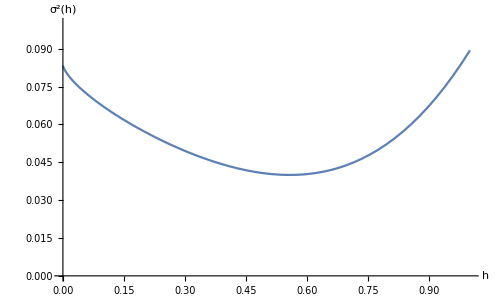

```mathematica
Plot[σ2h[h],{h,0,1},AxesLabel->{"h","σ^2(h)"},PlotRange->{0,.1}]
```

We can plot σ^2(h)'vs h and see that there is a zero with a sign change from negative to positive around h=.557

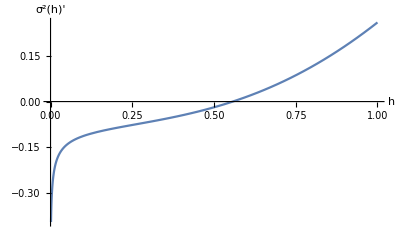

```mathematica
Plot[σ2h'[h],{h,0,1},AxesLabel->{"h","σ^2(h)'"}]
```

```mathematica
FindRoot[σ2h'[h],{h,.5}]
```

{h→0.557307}

## The New York Times and Mathematical Community

```mathematica
cv[h_]=Sqrt[σ2h[h]]/Abarh[h]
```

1/π 4 (ArcTan[1/h]-1/2 h Log[1+1/h^2]) √(-π^2/(16 (ArcTan[1/h]-1/2 h Log[1+1/h^2])^2)+(h+2 π+4 (1-h^2)^(3/2) ArcSin[h]-4 (1-h^2)^(3/2) ArcTan[(1+h)/(√(1-h^2))]+h^3 Log[4 h^2])/(6 (ArcTan[1/h]-1/2 h Log[1+1/h^2])))

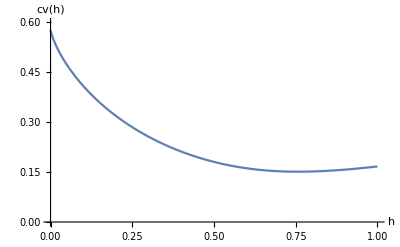

```mathematica
Plot[cv[h],{h,0,1},AxesLabel->{"h","cv(h)"},PlotRange->{0,.6}]
```

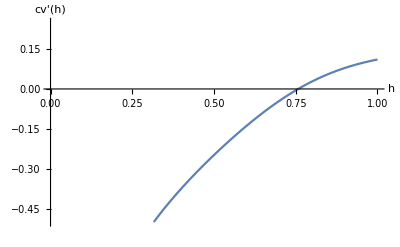

```mathematica
Plot[cv'[h],{h,0,1},AxesLabel->{"h","cv'(h)"},PlotRange->{-.5,.25}]
```

```mathematica
FindRoot[cv'[h],{h,.5}]
```

{h→0.757426}

## Three Dimensional Onions

c_h, x_h, y_h, and J_h from the paper:

```mathematica
ch[r_,ϕ_,z_,h_]:=h Cos[ϕ]+Sqrt[r^2-z^2-h^2 Sin[ϕ]^2];
xh[r_,ϕ_,z_,h_]:=ch[r,ϕ,z,h] Sin[ϕ];
yh[r_,ϕ_,z_,h_]:= ch[r,ϕ,z,h] Cos[ϕ]-h;
Jh[r_,ϕ_,z_,h_]:=D[xh[r,ϕ,z,h],r]D[yh[r,ϕ,z,h],ϕ]-D[xh[r,ϕ,z,h],ϕ]D[yh[r,ϕ,z,h],r]
```

Note that the absolute value of the Jacobian is the below expression with the absolute value removed, since r>h tan(θ) and tan(θ)>sin(θ) on this interval. Moreover, r>0,h>0 and cos(θ)>0.

```mathematica
FullSimplify[Jh[r,ϕ,z,h]]
```

r+(h r Cos[ϕ])/(√(r^2-z^2-h^2 Sin[ϕ]^2))

Let’s redefine Jh to be positive:

```mathematica
Jh[r_,ϕ_,z_,h_]:=r (1+(h Cos[ϕ])/(√(r^2-z^2-h^2 Sin[ϕ]^2)))
```

Simplifying the denominator doing the integrals from inside to outside.

```mathematica
Assuming[w>0&&w<1,Integrate[1,{r,Sqrt[h^2 Tan[θ]^2+w^2],1}]]
```

1-√(w^2+h^2 Tan[θ]^2)

```mathematica
Assuming[h>0&&w>0&&w<1,Integrate[1-√(w^2+h^2 Tan[ϕ]^2),{ϕ,0,ArcTan[Sqrt[1-w^2]/h]}]]
```

$Aborted

```mathematica
Assuming[h>0,Integrate[ArcCot[h/(√(1-w^2))]+√((h-w) (h+w)) (ArcCoth[(h √((h-w) (h+w)))/(1+h^2-w^2-√(1-w^2))]-ArcTanh[h/(√(h^2-w^2))])+h Log[(1-√(1-w^2))/w],{w,0,1}]]
```

∫_0^1 (ArcCot[h/(√(1-w^2))]+√((h-w) (h+w)) (ArcCoth[(h √((h-w) (h+w)))/(1+h^2-w^2-√(1-w^2))]-ArcTanh[h/(√(h^2-w^2))])+h Log[(1-√(1-w^2))/w])ⅆw

```mathematica
denom3D[h_]:=NIntegrate[(ArcCot[h/(√(1-w^2))]+√((h-w) (h+w)) (ArcCoth[(h √((h-w) (h+w)))/(1+h^2-w^2-√(1-w^2))]-ArcTanh[h/(√(h^2-w^2))])+h Log[(1-√(1-w^2))/w]),{w,0,1},Method->"GlobalAdaptive"]
```

```mathematica
Vbar[h_]:=(Pi/6)/denom3D[h]
```

The following code mimics the change to rectangular and then to polar of the integral of the square of the Jacobian.

Now, in anticipation of the square integral, we evaluate the Jacobian at r, θ, and w

```mathematica
Assuming[h>0&&x>0&&x<1&&y>0&&y<1&&z>0&&z<1,J[Sqrt[x^2+y^2+z^2],ArcTan[x/(y+h)],z,h]]
```

(1+h/(√(1+x^2/(h+y)^2) √(x^2+y^2-(h^2 x^2)/((h+y)^2 (1+x^2/(h+y)^2))))) √(x^2+y^2+z^2)

J in rectangular coordinates

```mathematica
JinRect[x_,y_,z_,h_]=(1+h/(√(1+x^2/(h+y)^2) √(x^2+y^2-(h^2 x^2)/((h+y)^2 (1+x^2/(h+y)^2))))) √(x^2+y^2+z^2)
```

(1+h/(√(1+x^2/(h+y)^2) √(x^2+y^2-(h^2 x^2)/((h+y)^2 (1+x^2/(h+y)^2))))) √(x^2+y^2+z^2)

Define spherical coordiantes

```mathematica
x[ρ_,ω_,ϕ_]=ρ Sin[ω]Cos[ϕ];
y[ρ_,ω_,ϕ_]=ρ Sin[ω]Sin[ϕ];
z[ρ_,ω_,ϕ_]=ρ Cos[ω];
```

```mathematica
JinRect[x[ρ,ω,ϕ],y[ρ,ω,ϕ],z[ρ,ω,ϕ],h]ρ^2Sin[ω]
```

ρ^2 Sin[ω] √(ρ^2 Cos[ω]^2+ρ^2 Cos[ϕ]^2 Sin[ω]^2+ρ^2 Sin[ϕ]^2 Sin[ω]^2) (1+h/(√(1+(ρ^2 Cos[ϕ]^2 Sin[ω]^2)/(h+ρ Sin[ϕ] Sin[ω])^2) √(ρ^2 Cos[ϕ]^2 Sin[ω]^2+ρ^2 Sin[ϕ]^2 Sin[ω]^2-(h^2 ρ^2 Cos[ϕ]^2 Sin[ω]^2)/((h+ρ Sin[ϕ] Sin[ω])^2 (1+(ρ^2 Cos[ϕ]^2 Sin[ω]^2)/(h+ρ Sin[ϕ] Sin[ω])^2)))))

```mathematica
Assuming[0<h&&0<ρ&&ρ<1&&0<ω&&ω<Pi/2&&0<ϕ&&ϕ<Pi/2,FullSimplify[ρ^2 Sin[ω] √(ρ^2 Cos[ω]^2+ρ^2 Cos[ϕ]^2 Sin[ω]^2+ρ^2 Sin[ϕ]^2 Sin[ω]^2) (1+h/(√(1+(ρ^2 Cos[ϕ]^2 Sin[ω]^2)/(h+ρ Sin[ϕ] Sin[ω])^2) √(ρ^2 Cos[ϕ]^2 Sin[ω]^2+ρ^2 Sin[ϕ]^2 Sin[ω]^2-(h^2 ρ^2 Cos[ϕ]^2 Sin[ω]^2)/((h+ρ Sin[ϕ] Sin[ω])^2 (1+(ρ^2 Cos[ϕ]^2 Sin[ω]^2)/(h+ρ Sin[ϕ] Sin[ω])^2)))))]]
```

(ρ^2 (h^2+ρ Sin[ω] (2 h Sin[ϕ]+ρ Sin[ω])))/(h Sin[ϕ]+ρ Sin[ω])

This is as good as Mathematica can symbolically manipulate the integral of J in spherical coordinates (which represents J^2 in the strange coordinate system)

```mathematica
Integrate[(ρ^2 (h^2+ρ Sin[ω] (2 h Sin[ϕ]+ρ Sin[ω])))/(h Sin[ϕ]+ρ Sin[ω]),{ρ,0,1},{ω,0,Pi/2},{ϕ,0,Pi/2}]
```

∫_0^1 ∫_0^(π/2) ρ^2 (√2 (ArcTan[(√2 h)/(√(-2 h^2+ρ^2-ρ^2 Cos[2 ω]))]-ArcTan[(√2 (h+ρ Sin[ω]))/(√(-2 h^2+ρ^2-ρ^2 Cos[2 ω]))]) √(-2 h^2+ρ^2-ρ^2 Cos[2 ω])+π ρ Sin[ω])ⅆωⅆρ

But, at least we have somewhat simplified the integral for the numerical algorithms...

```mathematica
numericalJsquared[h_]:=NIntegrate[ρ^2 (√2 (ArcTan[(√2 h)/(√(-2 h^2+ρ^2-ρ^2 Cos[2 ω]))]-ArcTan[(√2 (h+ρ Sin[ω]))/(√(-2 h^2+ρ^2-ρ^2 Cos[2 ω]))]) √(-2 h^2+ρ^2-ρ^2 Cos[2 ω])+π ρ Sin[ω]),{ω,0,Pi/2},{ρ,0,1},Method->"GlobalAdaptive"]
```

Define the variance as before, with the formula mimicking the formula for variance in terms of the mean and the second moment.

```mathematica
var[h_]:=numericalJsquared[h]/denom3DGlobal[h]-(Vbar[h])^2
```

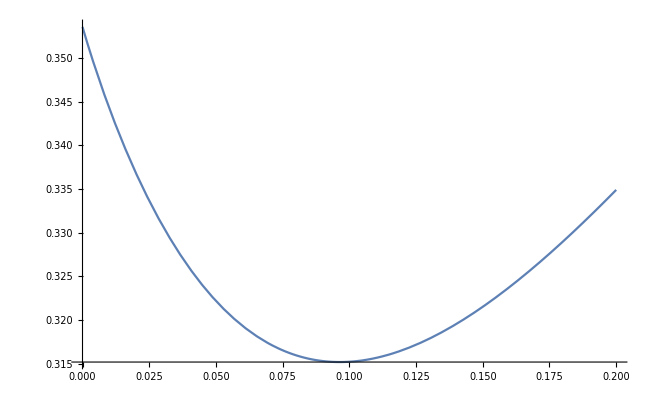

```mathematica
Plot[Sqrt[var[h]]/Vbar[h],{h,0,.2}]
```

```mathematica
NMinimize[Sqrt[var[h]]/Vbar[h],{h,0,.2}]
```

{0.315803,{h→0.0816575}}

This is the 3D onion constant for coefficient of variation!

The following code shows how we calculate for a cutoff. Here, cutoff =.75

```mathematica
cutoff=.75;
JSquaredCutoff[h_]:=NIntegrate[(J[r,θ,w,h])^2*Boole[r^2-w^2-h^2 Sin[θ]^2>0],{w,0,cutoff},{θ,0,ArcTan[Sqrt[1-w^2]/h]},{r,Sqrt[h^2 Tan[θ]^2+w^2],1},Method->{"GlobalAdaptive","MaxErrorIncreases"->30000},Exclusions->r^2-w^2-h^2 Sin[θ]^2==0]
```

Now the denominator (integral of 1 over the region)

```mathematica
denom3DCutoff[h_]:=NIntegrate[(ArcCot[h/(√(1-w^2))]+√((h-w) (h+w)) (ArcCoth[(h √((h-w) (h+w)))/(1+h^2-w^2-√(1-w^2))]-ArcTanh[h/(√(h^2-w^2))])+h Log[(1-√(1-w^2))/w]),{w,0,cutoff},Method->"GlobalAdaptive"]
```

We need to adjust the total volume of the onion by removing a spherical cap

```mathematica
sphericalCap[c_]=Pi(1-c)^2(3-(1-c))/3
VbarCutoff[h_]:=((2/3Pi-sphericalCap[cutoff])/4)/denom3DCutoff[h]
```

1/3 (1-c)^2 (2+c) π

This is slow to run...

```mathematica
ParallelTable[{h,Sqrt[JSquaredCutoff[h]/denom3DCutoff[h]-(VbarCutoff[h])^2]/VbarCutoff[h]},{h,0.001,0.75,0.001}]
```

{{0.001,0.358252},{0.002,0.357097},{0.003,0.355963},{0.004,0.354848},{0.005,0.353753},{0.006,0.352673},{0.007,0.351609},{0.008,0.350562},{0.009,0.349529},{0.01,0.348511},{0.011,0.347508},{0.012,0.346517},{0.013,0.345539},{0.014,0.344575},{0.015,0.343622},{0.016,0.342681},{0.017,0.341753},{0.018,0.340838},{0.019,0.339935},{0.02,0.339042},{0.021,0.338157},{0.022,0.337284},{0.023,0.336423},{0.024,0.335572},{0.025,0.334733},{0.026,0.333907},{0.027,0.333089},{0.028,0.332278},{0.029,0.331481},{0.03,0.330692},{0.031,0.329913},{0.032,0.329143},{0.033,0.328379},{0.034,0.327628},{0.035,0.326887},{0.036,0.326147},{0.037,0.325429},{0.038,0.324712},{0.039,0.324003},{0.04,0.323302},{0.041,0.322611},{0.042,0.321926},{0.043,0.321257},{0.044,0.320584},{0.045,0.319927},{0.046,0.319276},{0.047,0.318635},{0.048,0.317999},{0.049,0.317372},{0.05,0.316754},{0.051,0.316143},{0.052,0.315544},{0.053,0.314949},{0.054,0.31436},{0.055,0.313781},{0.056,0.313208},{0.057,0.312631},{0.058,0.312066},{0.059,0.311518},{0.06,0.310974},{0.061,0.310435},{0.062,0.309905},{0.063,0.309406},{0.064,0.308885},{0.065,0.308374},{0.066,0.307872},{0.067,0.307372},{0.068,0.306877},{0.069,0.306391},{0.07,0.305913},{0.071,0.305447},{0.072,0.304984},{0.073,0.304527},{0.074,0.304073},{0.075,0.303622},{0.076,0.303181},{0.077,0.30275},{0.078,0.302316},{0.079,0.301898},{0.08,0.301458},{0.081,0.301047},{0.082,0.300641},{0.083,0.300238},{0.084,0.299873},{0.085,0.299489},{0.086,0.299102},{0.087,0.29873},{0.088,0.298367},{0.089,0.297998},{0.09,0.297638},{0.091,0.297277},{0.092,0.296926},{0.093,0.296581},{0.094,0.296247},{0.095,0.29593},{0.096,0.2956},{0.097,0.29527},{0.098,0.294951},{0.099,0.294636},{0.1,0.294327},{0.101,0.293945},{0.102,0.293641},{0.103,0.293354},{0.104,0.293059},{0.105,0.292777},{0.106,0.292507},{0.107,0.292225},{0.108,0.291946},{0.109,0.291701},{0.11,0.291444},{0.111,0.291185},{0.112,0.290926},{0.113,0.290663},{0.114,0.290454},{0.115,0.290214},{0.116,0.289981},{0.117,0.289748},{0.118,0.289521},{0.119,0.289287},{0.12,0.289079},{0.121,0.288876},{0.122,0.28867},{0.123,0.28847},{0.124,0.288268},{0.125,0.288076},{0.126,0.287904},{0.127,0.287702},{0.128,0.287578},{0.129,0.287398},{0.13,0.287228},{0.131,0.287058},{0.132,0.286903},{0.133,0.286744},{0.134,0.286588},{0.135,0.286437},{0.136,0.286287},{0.137,0.28612},{0.138,0.286029},{0.139,0.285884},{0.14,0.285742},{0.141,0.285594},{0.142,0.285464},{0.143,0.285337},{0.144,0.28521},{0.145,0.285142},{0.146,0.285014},{0.147,0.284917},{0.148,0.284809},{0.149,0.284715},{0.15,0.284608},{0.151,0.284508},{0.152,0.28441},{0.153,0.284349},{0.154,0.284264},{0.155,0.284244},{0.156,0.284158},{0.157,0.284075},{0.158,0.284009},{0.159,0.283964},{0.16,0.283889},{0.161,0.283792},{0.162,0.283763},{0.163,0.283689},{0.164,0.28364},{0.165,0.283606},{0.166,0.283557},{0.167,0.283484},{0.168,0.28355},{0.169,0.283532},{0.17,0.283497},{0.171,0.283483},{0.172,0.283461},{0.173,0.283429},{0.174,0.283408},{0.175,0.283386},{0.176,0.28343},{0.177,0.283372},{0.178,0.283361},{0.179,0.283394},{0.18,0.28338},{0.181,0.283351},{0.182,0.283342},{0.183,0.283293},{0.184,0.28329},{0.185,0.283319},{0.186,0.283323},{0.187,0.283344},{0.188,0.283374},{0.189,0.283411},{0.19,0.283488},{0.191,0.28356},{0.192,0.283618},{0.193,0.283712},{0.194,0.283799},{0.195,0.28381},{0.196,0.283772},{0.197,0.283792},{0.198,0.283806},{0.199,0.283826},{0.2,0.283837},{0.201,0.283876},{0.202,0.283893},{0.203,0.283928},{0.204,0.283964},{0.205,0.283981},{0.206,0.283975},{0.207,0.283998},{0.208,0.28405},{0.209,0.284084},{0.21,0.28412},{0.211,0.284108},{0.212,0.284206},{0.213,0.284241},{0.214,0.284174},{0.215,0.284219},{0.216,0.284295},{0.217,0.284484},{0.218,0.284551},{0.219,0.284619},{0.22,0.284707},{0.221,0.284822},{0.222,0.284934},{0.223,0.285025},{0.224,0.285126},{0.225,0.285231},{0.226,0.285285},{0.227,0.285392},{0.228,0.28543},{0.229,0.28549},{0.23,0.285632},{0.231,0.285705},{0.232,0.285808},{0.233,0.285921},{0.234,0.286031},{0.235,0.28614},{0.236,0.286258},{0.237,0.286334},{0.238,0.286459},{0.239,0.286537},{0.24,0.286644},{0.241,0.286769},{0.242,0.28692},{0.243,0.286993},{0.244,0.287113},{0.245,0.287232},{0.246,0.287358},{0.247,0.287508},{0.248,0.287645},{0.249,0.287771},{0.25,0.287888},{0.251,0.288091},{0.252,0.288188},{0.253,0.288316},{0.254,0.288455},{0.255,0.288627},{0.256,0.288805},{0.257,0.288935},{0.258,0.289069},{0.259,0.289221},{0.26,0.289376},{0.261,0.28953},{0.262,0.289694},{0.263,0.289863},{0.264,0.290002},{0.265,0.290165},{0.266,0.29033},{0.267,0.290491},{0.268,0.290682},{0.269,0.290824},{0.27,0.290989},{0.271,0.29114},{0.272,0.291307},{0.273,0.291465},{0.274,0.291675},{0.275,0.291833},{0.276,0.292017},{0.277,0.292147},{0.278,0.292312},{0.279,0.292485},{0.28,0.292537},{0.281,0.292648},{0.282,0.292793},{0.283,0.292976},{0.284,0.293135},{0.285,0.293305},{0.286,0.293454},{0.287,0.293599},{0.288,0.29377},{0.289,0.294236},{0.29,0.294414},{0.291,0.294573},{0.292,0.29473},{0.293,0.294842},{0.294,0.294996},{0.295,0.295242},{0.296,0.29546},{0.297,0.295596},{0.298,0.295814},{0.299,0.296003},{0.3,0.296191},{0.301,0.296446},{0.302,0.296694},{0.303,0.296879},{0.304,0.297054},{0.305,0.297268},{0.306,0.297446},{0.307,0.297643},{0.308,0.29785},{0.309,0.298189},{0.31,0.29844},{0.311,0.298633},{0.312,0.298824},{0.313,0.299034},{0.314,0.299213},{0.315,0.29937},{0.316,0.299575},{0.317,0.299758},{0.318,0.299974},{0.319,0.300148},{0.32,0.30035},{0.321,0.300541},{0.322,0.300749},{0.323,0.300935},{0.324,0.301097},{0.325,0.301266},{0.326,0.301443},{0.327,0.301657},{0.328,0.301802},{0.329,0.30203},{0.33,0.302227},{0.331,0.302464},{0.332,0.302673},{0.333,0.302871},{0.334,0.303093},{0.335,0.30331},{0.336,0.303561},{0.337,0.303789},{0.338,0.304086},{0.339,0.304263},{0.34,0.30448},{0.341,0.304705},{0.342,0.304938},{0.343,0.305146},{0.344,0.305324},{0.345,0.305559},{0.346,0.305758},{0.347,0.305987},{0.348,0.306203},{0.349,0.306457},{0.35,0.30669},{0.351,0.306973},{0.352,0.307155},{0.353,0.307398},{0.354,0.30763},{0.355,0.307833},{0.356,0.308053},{0.357,0.3083},{0.358,0.308519},{0.359,0.308755},{0.36,0.309044},{0.361,0.309317},{0.362,0.309486},{0.363,0.309725},{0.364,0.309948},{0.365,0.309948},{0.366,0.310207},{0.367,0.310433},{0.368,0.310682},{0.369,0.310914},{0.37,0.311159},{0.371,0.311223},{0.372,0.311487},{0.373,0.311722},{0.374,0.311823},{0.375,0.312157},{0.376,0.312396},{0.377,0.312693},{0.378,0.312886},{0.379,0.313061},{0.38,0.313347},{0.381,0.313641},{0.382,0.313972},{0.383,0.314295},{0.384,0.314653},{0.385,0.315002},{0.386,0.31534},{0.387,0.31587},{0.388,0.316051},{0.389,0.316375},{0.39,0.316561},{0.391,0.31667},{0.392,0.316859},{0.393,0.317116},{0.394,0.317308},{0.395,0.31752},{0.396,0.317711},{0.397,0.317931},{0.398,0.31813},{0.399,0.318303},{0.4,0.318422},{0.401,0.318607},{0.402,0.318795},{0.403,0.319013},{0.404,0.319218},{0.405,0.319396},{0.406,0.319576},{0.407,0.319763},{0.408,0.319977},{0.409,0.32023},{0.41,0.320427},{0.411,0.320618},{0.412,0.320826},{0.413,0.321024},{0.414,0.321289},{0.415,0.321531},{0.416,0.321704},{0.417,0.321915},{0.418,0.322078},{0.419,0.322189},{0.42,0.32236},{0.421,0.322392},{0.422,0.322514},{0.423,0.322746},{0.424,0.322993},{0.425,0.323236},{0.426,0.32352},{0.427,0.323711},{0.428,0.323556},{0.429,0.323805},{0.43,0.324054},{0.431,0.324259},{0.432,0.324511},{0.433,0.324776},{0.434,0.324967},{0.435,0.325201},{0.436,0.325399},{0.437,0.325542},{0.438,0.325785},{0.439,0.326025},{0.44,0.326275},{0.441,0.326527},{0.442,0.326785},{0.443,0.327108},{0.444,0.327361},{0.445,0.327605},{0.446,0.327846},{0.447,0.328096},{0.448,0.328364},{0.449,0.328605},{0.45,0.328845},{0.451,0.32907},{0.452,0.329369},{0.453,0.329645},{0.454,0.329879},{0.455,0.330178},{0.456,0.330422},{0.457,0.330625},{0.458,0.330732},{0.459,0.330986},{0.46,0.33127},{0.461,0.331591},{0.462,0.331832},{0.463,0.332097},{0.464,0.332318},{0.465,0.332569},{0.466,0.332793},{0.467,0.333052},{0.468,0.333264},{0.469,0.333471},{0.47,0.333742},{0.471,0.333983},{0.472,0.334211},{0.473,0.334468},{0.474,0.334727},{0.475,0.334972},{0.476,0.335221},{0.477,0.335403},{0.478,0.335581},{0.479,0.335884},{0.48,0.336139},{0.481,0.336371},{0.482,0.336713},{0.483,0.336968},{0.484,0.337166},{0.485,0.337379},{0.486,0.337467},{0.487,0.337631},{0.488,0.337823},{0.489,0.338112},{0.49,0.338395},{0.491,0.338691},{0.492,0.338948},{0.493,0.339202},{0.494,0.339421},{0.495,0.339837},{0.496,0.340037},{0.497,0.340244},{0.498,0.34047},{0.499,0.340727},{0.5,0.340671},{0.501,0.340843},{0.502,0.341101},{0.503,0.341171},{0.504,0.341359},{0.505,0.341622},{0.506,0.341849},{0.507,0.342221},{0.508,0.342466},{0.509,0.342785},{0.51,0.343047},{0.511,0.34328},{0.512,0.34353},{0.513,0.34383},{0.514,0.343852},{0.515,0.344091},{0.516,0.344313},{0.517,0.344569},{0.518,0.344789},{0.519,0.344989},{0.52,0.34523},{0.521,0.345501},{0.522,0.34577},{0.523,0.345939},{0.524,0.346191},{0.525,0.346524},{0.526,0.346769},{0.527,0.347002},{0.528,0.347185},{0.529,0.347381},{0.53,0.347641},{0.531,0.347872},{0.532,0.348025},{0.533,0.348212},{0.534,0.348477},{0.535,0.34874},{0.536,0.348956},{0.537,0.349172},{0.538,0.34945},{0.539,0.349681},{0.54,0.349926},{0.541,0.350262},{0.542,0.350468},{0.543,0.350717},{0.544,0.350904},{0.545,0.351173},{0.546,0.351465},{0.547,0.351657},{0.548,0.352033},{0.549,0.352249},{0.55,0.352511},{0.551,0.352675},{0.552,0.352943},{0.553,0.353174},{0.554,0.353396},{0.555,0.353718},{0.556,0.353964},{0.557,0.35423},{0.558,0.354472},{0.559,0.354656},{0.56,0.354917},{0.561,0.354994},{0.562,0.355208},{0.563,0.355342},{0.564,0.355594},{0.565,0.355826},{0.566,0.356057},{0.567,0.35628},{0.568,0.356513},{0.569,0.356703},{0.57,0.356736},{0.571,0.35699},{0.572,0.357194},{0.573,0.35742},{0.574,0.357646},{0.575,0.357894},{0.576,0.358134},{0.577,0.358361},{0.578,0.358578},{0.579,0.358821},{0.58,0.359039},{0.581,0.359266},{0.582,0.359486},{0.583,0.35972},{0.584,0.359826},{0.585,0.360057},{0.586,0.360343},{0.587,0.360551},{0.588,0.360809},{0.589,0.361021},{0.59,0.361296},{0.591,0.361546},{0.592,0.3617},{0.593,0.361925},{0.594,0.362197},{0.595,0.362447},{0.596,0.362665},{0.597,0.362888},{0.598,0.36313},{0.599,0.363283},{0.6,0.363521},{0.601,0.363732},{0.602,0.363945},{0.603,0.364136},{0.604,0.364314},{0.605,0.364322},{0.606,0.364522},{0.607,0.364738},{0.608,0.364964},{0.609,0.365165},{0.61,0.365368},{0.611,0.365482},{0.612,0.365723},{0.613,0.365938},{0.614,0.366401},{0.615,0.366643},{0.616,0.366842},{0.617,0.366456},{0.618,0.36668},{0.619,0.366909},{0.62,0.367119},{0.621,0.367329},{0.622,0.36751},{0.623,0.36768},{0.624,0.36789},{0.625,0.368064},{0.626,0.368294},{0.627,0.368526},{0.628,0.368758},{0.629,0.368995},{0.63,0.369049},{0.631,0.3693},{0.632,0.369565},{0.633,0.36976},{0.634,0.370001},{0.635,0.370295},{0.636,0.370514},{0.637,0.370746},{0.638,0.370943},{0.639,0.371118},{0.64,0.371342},{0.641,0.371554},{0.642,0.371733},{0.643,0.37245},{0.644,0.372756},{0.645,0.372915},{0.646,0.373106},{0.647,0.373265},{0.648,0.373425},{0.649,0.37361},{0.65,0.373734},{0.651,0.373917},{0.652,0.374139},{0.653,0.374357},{0.654,0.374598},{0.655,0.374348},{0.656,0.374611},{0.657,0.374844},{0.658,0.374356},{0.659,0.374629},{0.66,0.374776},{0.661,0.375065},{0.662,0.375285},{0.663,0.375511},{0.664,0.376094},{0.665,0.376351},{0.666,0.376667},{0.667,0.376928},{0.668,0.377164},{0.669,0.377403},{0.67,0.377633},{0.671,0.377898},{0.672,0.378137},{0.673,0.378378},{0.674,0.378601},{0.675,0.37885},{0.676,0.379423},{0.677,0.379672},{0.678,0.379754},{0.679,0.379981},{0.68,0.380201},{0.681,0.380441},{0.682,0.380545},{0.683,0.38076},{0.684,0.380951},{0.685,0.381696},{0.686,0.381996},{0.687,0.381752},{0.688,0.381981},{0.689,0.38242},{0.69,0.382653},{0.691,0.382851},{0.692,0.383087},{0.693,0.38328},{0.694,0.383577},{0.695,0.383812},{0.696,0.383984},{0.697,0.384201},{0.698,0.384511},{0.699,0.384781},{0.7,0.385065},{0.701,0.385311},{0.702,0.385564},{0.703,0.385777},{0.704,0.386055},{0.705,0.386355},{0.706,0.386694},{0.707,0.386912},{0.708,0.387112},{0.709,0.387318},{0.71,0.387453},{0.711,0.387641},{0.712,0.38784},{0.713,0.388056},{0.714,0.388385},{0.715,0.388521},{0.716,0.38866},{0.717,0.388893},{0.718,0.389101},{0.719,0.389289},{0.72,0.389487},{0.721,0.389852},{0.722,0.390089},{0.723,0.390286},{0.724,0.390452},{0.725,0.390657},{0.726,0.390869},{0.727,0.391043},{0.728,0.391465},{0.729,0.391661},{0.73,0.391296},{0.731,0.391524},{0.732,0.391819},{0.733,0.392006},{0.734,0.392207},{0.735,0.392464},{0.736,0.392877},{0.737,0.393117},{0.738,0.393357},{0.739,0.393584},{0.74,0.3938},{0.741,0.39379},{0.742,0.394004},{0.743,0.394653},{0.744,0.394865},{0.745,0.395109},{0.746,0.395345},{0.747,0.395626},{0.748,0.395851},{0.749,0.396259},{0.75,0.396311}}

and we can make a plot from the output

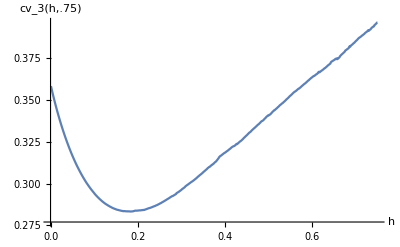

```mathematica
ListLinePlot[{{0.001,0.3582523047216608},{0.002,0.3570965570142266},{0.003,0.3559627343099248},{0.004,0.35484841133380574},{0.005,0.35375251192702817},{0.006,0.35267330716947604},{0.007,0.3516094829109243},{0.008,0.35056198579705017},{0.009000000000000001,0.34952882229561005},{0.010000000000000002,0.3485112485095024},{0.011,0.3475077890030281},{0.012,0.3465171281419932},{0.013000000000000001,0.3455388866749358},{0.014000000000000002,0.3445748144872693},{0.015,0.3436220718081856},{0.016,0.3426808344288158},{0.017,0.34175270293699855},{0.018000000000000002,0.34083807533199284},{0.019000000000000003,0.33993515364886473},{0.02,0.3390416820702403},{0.021,0.33815657203665844},{0.022,0.33728364095458435},{0.023,0.3364231059567543},{0.024,0.3355722974778038},{0.025,0.3347334741424855},{0.026000000000000002,0.33390734295726127},{0.027,0.3330887634670436},{0.028,0.33227789269578617},{0.029,0.3314807087552345},{0.03,0.3306924814555316},{0.031,0.3299127341545254},{0.032,0.3291430851782488},{0.033,0.32837901793940466},{0.034,0.32762755064561266},{0.035,0.3268867890436702},{0.036000000000000004,0.32614691978499344},{0.037000000000000005,0.3254285926699335},{0.038000000000000006,0.3247120996747094},{0.039,0.3240032132460506},{0.04,0.3233021912782641},{0.041,0.3226107777525627},{0.042,0.32192583948406794},{0.043,0.32125675954215793},{0.044,0.32058362500897103},{0.045,0.31992709485686754},{0.046,0.31927599507925075},{0.047,0.31863486749726},{0.048,0.3179988781550362},{0.049,0.31737236752601733},{0.05,0.31675382561238197},{0.051000000000000004,0.31614301265430805},{0.052000000000000005,0.31554389463627863},{0.053,0.31494856484333456},{0.054,0.31436047107698184},{0.055,0.31378131184503993},{0.056,0.31320811069267784},{0.057,0.3126306989227301},{0.058,0.3120660353161753},{0.059000000000000004,0.3115179460414669},{0.060000000000000005,0.31097379686902754},{0.061000000000000006,0.3104353155425185},{0.062,0.30990549382890664},{0.063,0.3094063075094457},{0.064,0.30888514248205645},{0.065,0.3083739326044149},{0.066,0.30787173183543887},{0.067,0.3073720229176821},{0.068,0.306876619274592},{0.069,0.3063914773720834},{0.07,0.30591306602082197},{0.07100000000000001,0.3054473137030462},{0.07200000000000001,0.3049843283924627},{0.07300000000000001,0.3045265114539513},{0.07400000000000001,0.3040728600636169},{0.07500000000000001,0.30362171080328904},{0.07600000000000001,0.3031811121411402},{0.077,0.30274953789410003},{0.078,0.3023160286494953},{0.079,0.30189848535579605},{0.08,0.30145786871241415},{0.081,0.3010468161157061},{0.082,0.30064065204611845},{0.083,0.30023848331871694},{0.084,0.29987307660480217},{0.08499999999999999,0.2994889548068887},{0.086,0.29910187195378124},{0.087,0.29872953588391504},{0.088,0.29836701326401593},{0.089,0.29799828577898774},{0.09,0.2976378088379613},{0.091,0.2972773909082939},{0.092,0.29692618616738287},{0.093,0.29658085457135},{0.094,0.2962472928995935},{0.095,0.2959301133703593},{0.096,0.2956002281727557},{0.097,0.29527021230468686},{0.098,0.29495135144384665},{0.099,0.2946362755834269},{0.1,0.29432740943115776},{0.101,0.2939445804377464},{0.10200000000000001,0.2936413506622728},{0.10300000000000001,0.29335431210927676},{0.10400000000000001,0.2930591851491862},{0.10500000000000001,0.2927774134410802},{0.106,0.2925072796350758},{0.107,0.2922248251525125},{0.108,0.2919457705965336},{0.109,0.29170060866345887},{0.11,0.29144375743497714},{0.111,0.29118528520416254},{0.112,0.29092615959088125},{0.113,0.29066266130986657},{0.114,0.29045404426041554},{0.115,0.2902142700394538},{0.116,0.28998132602236204},{0.117,0.2897475240019936},{0.11800000000000001,0.2895213334286542},{0.11900000000000001,0.2892872614095421},{0.12000000000000001,0.28907853306535564},{0.12100000000000001,0.28887599887928916},{0.12200000000000001,0.28867041536205623},{0.123,0.2884703041318263},{0.124,0.2882682460479228},{0.125,0.28807643931599847},{0.126,0.28790361364361416},{0.127,0.2877017049153947},{0.128,0.28757801139829786},{0.129,0.28739840157632157},{0.13,0.28722816621979785},{0.131,0.28705833254564567},{0.132,0.28690324067784106},{0.133,0.2867444333202426},{0.134,0.28658785160527533},{0.135,0.2864365440924996},{0.136,0.2862873770760992},{0.137,0.28612048806870016},{0.138,0.28602920641443924},{0.139,0.28588405283687307},{0.14,0.2857415775312236},{0.14100000000000001,0.2855940016176262},{0.14200000000000002,0.2854635557286826},{0.14300000000000002,0.2853373898624412},{0.14400000000000002,0.28520991624634295},{0.14500000000000002,0.28514204263526105},{0.14600000000000002,0.2850136277255346},{0.14700000000000002,0.28491659216290444},{0.14800000000000002,0.2848089107776604},{0.14900000000000002,0.28471488663419237},{0.15000000000000002,0.28460802065166796},{0.15100000000000002,0.2845078189857235},{0.15200000000000002,0.28441001853088105},{0.153,0.2843494046049654},{0.154,0.28426357516289824},{0.155,0.2842443082517699},{0.156,0.2841583598344442},{0.157,0.28407476558690037},{0.158,0.2840086776557042},{0.159,0.28396431156330837},{0.16,0.28388887307611954},{0.161,0.2837923218629644},{0.162,0.28376346586762047},{0.163,0.2836889891560439},{0.164,0.2836395165268237},{0.165,0.28360597808786703},{0.166,0.2835568273678729},{0.167,0.28348375073242593},{0.16799999999999998,0.2835501465030145},{0.16899999999999998,0.28353211745998924},{0.16999999999999998,0.28349652024532146},{0.17099999999999999,0.2834830264618998},{0.17200000000000001,0.2834607707731496},{0.17300000000000001,0.28342946834264793},{0.17400000000000002,0.2834082938779183},{0.17500000000000002,0.2833856467879352},{0.17600000000000002,0.28343031050480694},{0.17700000000000002,0.2833717930456908},{0.17800000000000002,0.28336138504610225},{0.17900000000000002,0.28339365345730255},{0.18000000000000002,0.283380168078134},{0.18100000000000002,0.28335146175242504},{0.18200000000000002,0.28334248868591266},{0.18300000000000002,0.283292538167039},{0.18400000000000002,0.2832899727025533},{0.18500000000000003,0.2833187895070772},{0.18600000000000003,0.2833227407059958},{0.187,0.28334361119452417},{0.188,0.283373706954827},{0.189,0.2834105171325531},{0.19,0.2834876815187298},{0.191,0.2835597971658762},{0.192,0.2836177057932795},{0.193,0.28371163457085335},{0.194,0.28379908696132095},{0.195,0.28380979015308605},{0.196,0.2837718763293603},{0.197,0.28379194541864605},{0.198,0.28380597895000687},{0.199,0.2838264999918607},{0.2,0.2838365384715067},{0.201,0.28387639075747745},{0.202,0.2838928062384649},{0.203,0.28392812758996605},{0.20400000000000001,0.28396393590870095},{0.20500000000000002,0.28398138120569466},{0.20600000000000002,0.2839747441472523},{0.20700000000000002,0.2839976419355138},{0.20800000000000002,0.2840496928487964},{0.20900000000000002,0.2840842200149369},{0.21,0.2841198339794847},{0.211,0.28410822442841027},{0.212,0.28420603326739385},{0.213,0.2842411581881073},{0.214,0.2841740106904984},{0.215,0.2842186432169739},{0.216,0.2842953779546902},{0.217,0.28448417313662666},{0.218,0.28455068693575253},{0.219,0.28461910696448617},{0.22,0.2847072620572855},{0.221,0.2848216665296211},{0.222,0.28493358572896166},{0.223,0.2850245160425873},{0.224,0.28512584087281173},{0.22499999999999998,0.28523118219668314},{0.22599999999999998,0.2852851265913755},{0.22699999999999998,0.2853917582602909},{0.22799999999999998,0.2854301926698241},{0.229,0.28549038441243707},{0.23,0.2856322644861092},{0.231,0.28570510564813695},{0.232,0.28580831521573885},{0.233,0.2859209500483061},{0.234,0.2860305559513814},{0.23500000000000001,0.2861404622907605},{0.23600000000000002,0.2862575559488138},{0.23700000000000002,0.2863336529387096},{0.23800000000000002,0.2864587097967867},{0.23900000000000002,0.2865369919393407},{0.24000000000000002,0.28664434924506804},{0.24100000000000002,0.28676900545402356},{0.24200000000000002,0.28692009192851387},{0.24300000000000002,0.28699335505347606},{0.244,0.28711329385891504},{0.245,0.28723215996965756},{0.246,0.28735770225085333},{0.247,0.2875083026212689},{0.248,0.2876449192837689},{0.249,0.2877705423372398},{0.25,0.28788807785258985},{0.251,0.28809064948662005},{0.252,0.2881878765967849},{0.253,0.2883159032184135},{0.254,0.2884547855393068},{0.255,0.2886265091922697},{0.256,0.2888046799556343},{0.257,0.2889354364778955},{0.258,0.28906934575666005},{0.259,0.28922137948175275},{0.26,0.2893764240881061},{0.261,0.2895301621156939},{0.262,0.28969366758234505},{0.263,0.2898628882924681},{0.264,0.29000176195254496},{0.265,0.2901653121081147},{0.266,0.2903298607673525},{0.267,0.29049111859256177},{0.268,0.2906820964168032},{0.269,0.2908240960550972},{0.27,0.2909891492009355},{0.271,0.29113955576230094},{0.272,0.29130651739109487},{0.273,0.2914654413724377},{0.274,0.2916749273445593},{0.275,0.29183347849198304},{0.276,0.2920165284032516},{0.277,0.29214706204706314},{0.278,0.29231195940980953},{0.279,0.2924845073592882},{0.28,0.292537494382708},{0.281,0.29264847207234196},{0.28200000000000003,0.2927928630169525},{0.28300000000000003,0.2929759903868665},{0.28400000000000003,0.29313539582709225},{0.28500000000000003,0.29330500725406505},{0.28600000000000003,0.29345417735930696},{0.28700000000000003,0.2935992683726566},{0.28800000000000003,0.29376986541792893},{0.28900000000000003,0.29423594446519635},{0.29000000000000004,0.29441394021289546},{0.29100000000000004,0.29457257960030897},{0.29200000000000004,0.2947302271785677},{0.29300000000000004,0.2948422452479882},{0.29400000000000004,0.29499561722023615},{0.29500000000000004,0.29524157156310377},{0.29600000000000004,0.2954600423978774},{0.29700000000000004,0.2955955664729412},{0.29800000000000004,0.2958142613736337},{0.29900000000000004,0.2960025605215209},{0.30000000000000004,0.29619119585969733},{0.30100000000000005,0.29644603070802966},{0.30200000000000005,0.29669440523342744},{0.30300000000000005,0.29687872542520993},{0.30400000000000005,0.2970543977210818},{0.305,0.29726752879107954},{0.306,0.2974456817002523},{0.307,0.2976431765612766},{0.308,0.29784973762696204},{0.309,0.29818878388764486},{0.31,0.29843963423390923},{0.311,0.298632694562163},{0.312,0.2988239817811742},{0.313,0.2990337682642343},{0.314,0.29921335325559145},{0.315,0.299370377707692},{0.316,0.2995754017695623},{0.317,0.29975829440394597},{0.318,0.29997447751874656},{0.319,0.3001478481487058},{0.32,0.3003504972186215},{0.321,0.30054118878380737},{0.322,0.3007491560417836},{0.323,0.3009352579736345},{0.324,0.30109656414736324},{0.325,0.3012662151408548},{0.326,0.30144253746274213},{0.327,0.30165710265757756},{0.328,0.30180165992089736},{0.329,0.3020300447129533},{0.33,0.30222738239356783},{0.331,0.3024635511745015},{0.332,0.30267277908983115},{0.333,0.30287089271166445},{0.334,0.3030928514707875},{0.335,0.30330983662365585},{0.336,0.3035612831297105},{0.337,0.30378893849992805},{0.338,0.3040860610535037},{0.339,0.30426292203912236},{0.34,0.3044796515188925},{0.341,0.3047052341704799},{0.342,0.3049378358539147},{0.343,0.30514623259358453},{0.34400000000000003,0.3053244021681299},{0.34500000000000003,0.3055592475700197},{0.34600000000000003,0.30575797223148327},{0.34700000000000003,0.3059867075058978},{0.34800000000000003,0.3062031466848254},{0.34900000000000003,0.30645741686761546},{0.35000000000000003,0.30669006519428926},{0.35100000000000003,0.3069734254283028},{0.35200000000000004,0.3071548954769458},{0.35300000000000004,0.30739786324015594},{0.35400000000000004,0.30762974741519594},{0.35500000000000004,0.3078329423397415},{0.35600000000000004,0.30805276050194785},{0.35700000000000004,0.3083004520011385},{0.35800000000000004,0.30851927723572475},{0.35900000000000004,0.3087546841587307},{0.36000000000000004,0.3090442476438003},{0.36100000000000004,0.30931743145400004},{0.362,0.30948602651972645},{0.363,0.3097247743198278},{0.364,0.3099484386743873},{0.365,0.3099475720701926},{0.366,0.3102072349208769},{0.367,0.31043328553866234},{0.368,0.3106820410867285},{0.369,0.310914442525113},{0.37,0.31115903548695373},{0.371,0.31122262502024894},{0.372,0.31148706107095625},{0.373,0.31172206417136106},{0.374,0.31182324256910615},{0.375,0.31215657264442176},{0.376,0.31239590340976936},{0.377,0.3126926057093101},{0.378,0.3128863252425896},{0.379,0.3130612054816342},{0.38,0.31334740556913354},{0.381,0.3136406605230375},{0.382,0.31397242496711025},{0.383,0.3142950008417815},{0.384,0.3146530676499383},{0.385,0.3150019556565134},{0.386,0.31533982842274544},{0.387,0.315869997012096},{0.388,0.3160511293846213},{0.389,0.3163751496472967},{0.39,0.3165613548409585},{0.391,0.3166704358147024},{0.392,0.31685949438903893},{0.393,0.31711601346770135},{0.394,0.31730796913474074},{0.395,0.31752031506091916},{0.396,0.3177109598498342},{0.397,0.3179312459980435},{0.398,0.31813025473188244},{0.399,0.31830327621491755},{0.4,0.31842172832756604},{0.401,0.31860717333351407},{0.402,0.31879510385681886},{0.403,0.3190131991643905},{0.404,0.31921797516176487},{0.405,0.31939552739807375},{0.406,0.31957632314406625},{0.40700000000000003,0.31976349297315004},{0.40800000000000003,0.3199767455098612},{0.40900000000000003,0.3202299100265339},{0.41000000000000003,0.32042721949059366},{0.41100000000000003,0.32061759357145103},{0.41200000000000003,0.3208262419106595},{0.41300000000000003,0.32102418825731954},{0.41400000000000003,0.3212889707318883},{0.41500000000000004,0.32153122267697193},{0.41600000000000004,0.3217035615014418},{0.41700000000000004,0.32191497249904194},{0.41800000000000004,0.3220782992310971},{0.419,0.3221886045576229},{0.42,0.3223597332732741},{0.421,0.3223919068931179},{0.422,0.3225142765974649},{0.423,0.32274630926137166},{0.424,0.3229929348126655},{0.425,0.3232363628995395},{0.426,0.3235195845199138},{0.427,0.3237111905945554},{0.428,0.3235556795481207},{0.429,0.32380521096845344},{0.43,0.3240544456347642},{0.431,0.32425859481228825},{0.432,0.3245105959040631},{0.433,0.32477644544121353},{0.434,0.3249666402288792},{0.435,0.3252008120636703},{0.436,0.32539921728201626},{0.437,0.3255422572509382},{0.438,0.32578468998909244},{0.439,0.3260252859149059},{0.44,0.32627464813733686},{0.441,0.3265274809948141},{0.442,0.32678489300613056},{0.443,0.32710798933594215},{0.444,0.32736071030773645},{0.445,0.32760464537506423},{0.446,0.3278455845429456},{0.447,0.3280961596978366},{0.448,0.32836416570176163},{0.449,0.328605123882474},{0.45,0.32884511144444645},{0.451,0.32906996894799684},{0.452,0.32936860736668394},{0.453,0.32964461393430844},{0.454,0.32987852096536147},{0.455,0.33017818650469116},{0.456,0.33042163833232013},{0.457,0.33062546659960945},{0.458,0.33073196664191695},{0.459,0.33098571559743106},{0.46,0.3312697835574758},{0.461,0.33159073327296196},{0.462,0.33183166843730244},{0.463,0.33209706418296886},{0.464,0.33231798658773676},{0.465,0.33256930432616605},{0.466,0.33279276600870555},{0.467,0.3330523743391231},{0.468,0.33326358835231584},{0.46900000000000003,0.3334705804065195},{0.47000000000000003,0.3337421865922092},{0.47100000000000003,0.33398314322401607},{0.47200000000000003,0.33421142210734045},{0.47300000000000003,0.3344681718344757},{0.47400000000000003,0.3347269416286811},{0.47500000000000003,0.334972245448563},{0.47600000000000003,0.3352209320153833},{0.47700000000000004,0.33540289779293053},{0.47800000000000004,0.3355805042932609},{0.47900000000000004,0.33588404888974205},{0.48000000000000004,0.33613879303657307},{0.48100000000000004,0.33637050050943995},{0.48200000000000004,0.33671282750677506},{0.48300000000000004,0.3369677578789871},{0.48400000000000004,0.3371664337502854},{0.48500000000000004,0.3373789222395349},{0.48600000000000004,0.33746677929340707},{0.48700000000000004,0.33763140359134625},{0.48800000000000004,0.3378226431943642},{0.48900000000000005,0.3381119971036764},{0.49000000000000005,0.33839547021225946},{0.49100000000000005,0.33869097058788894},{0.49200000000000005,0.3389475198904918},{0.49300000000000005,0.3392017229238842},{0.49400000000000005,0.33942086826066464},{0.495,0.33983708879179486},{0.496,0.3400369268312135},{0.497,0.3402438380425453},{0.498,0.3404702329859156},{0.499,0.3407273691619617},{0.5,0.3406705257723882},{0.501,0.34084254174509265},{0.502,0.34110052619158115},{0.503,0.3411708625518206},{0.504,0.3413592923761781},{0.505,0.3416215547410938},{0.506,0.34184865361789735},{0.507,0.34222118176259214},{0.508,0.3424658638155579},{0.509,0.34278468179454},{0.51,0.34304729215105073},{0.511,0.34328029520230985},{0.512,0.34353022698925895},{0.513,0.3438297116313489},{0.514,0.34385155578932036},{0.515,0.34409110626051015},{0.516,0.344312918156047},{0.517,0.3445687186686099},{0.518,0.34478883794257925},{0.519,0.34498889873288896},{0.52,0.34522970637680084},{0.521,0.3455009071253521},{0.522,0.3457695850218451},{0.523,0.34593911906533664},{0.524,0.3461914720852224},{0.525,0.3465241846026777},{0.526,0.34676892269725},{0.527,0.34700211842222867},{0.528,0.34718540460947206},{0.529,0.3473812166121284},{0.53,0.3476405244162478},{0.531,0.34787184564606777},{0.532,0.34802504590310723},{0.533,0.3482119958300957},{0.534,0.34847749107626286},{0.535,0.3487402284151641},{0.536,0.3489555270711455},{0.537,0.34917227846577253},{0.538,0.3494503156993652},{0.539,0.34968135369176157},{0.54,0.34992626949048833},{0.541,0.35026152612740874},{0.542,0.3504684019326324},{0.543,0.35071721214210794},{0.544,0.35090444973520246},{0.545,0.35117271049816046},{0.546,0.3514651338359871},{0.547,0.35165715695149086},{0.548,0.3520326172368926},{0.549,0.3522486973109837},{0.55,0.3525105360533702},{0.551,0.3526746860244594},{0.552,0.35294267562302417},{0.553,0.3531736079084837},{0.554,0.35339574244973043},{0.555,0.3537175259234429},{0.556,0.3539636256728644},{0.557,0.3542302060025515},{0.558,0.35447205061857245},{0.559,0.35465562229547526},{0.56,0.35491672423400783},{0.561,0.35499448181578164},{0.562,0.3552083742169214},{0.5630000000000001,0.35534248114270384},{0.5640000000000001,0.35559428157282863},{0.5650000000000001,0.3558257338374129},{0.5660000000000001,0.35605677787897205},{0.5670000000000001,0.3562797721284962},{0.5680000000000001,0.3565125856754139},{0.5690000000000001,0.3567031928228566},{0.5700000000000001,0.35673583984304447},{0.5710000000000001,0.3569900819961726},{0.5720000000000001,0.3571940875415388},{0.5730000000000001,0.3574195054024432},{0.5740000000000001,0.3576464854555001},{0.5750000000000001,0.3578937805647458},{0.5760000000000001,0.3581344756437799},{0.5770000000000001,0.3583605893529992},{0.5780000000000001,0.3585778416254658},{0.5790000000000001,0.35882063557955846},{0.5800000000000001,0.35903936060412767},{0.5810000000000001,0.35926624376541816},{0.5820000000000001,0.35948571652642336},{0.5830000000000001,0.35972026352242137},{0.5840000000000001,0.3598258452330717},{0.5850000000000001,0.360056766410453},{0.5860000000000001,0.36034291142525643},{0.5870000000000001,0.360550896026474},{0.5880000000000001,0.3608093479460809},{0.589,0.3610212548938664},{0.59,0.36129644201911726},{0.591,0.36154578414816346},{0.592,0.36170014498895925},{0.593,0.36192517677063074},{0.594,0.362197240511594},{0.595,0.3624469451007909},{0.596,0.36266535975359493},{0.597,0.36288760564035016},{0.598,0.36312977384709133},{0.599,0.363283037485318},{0.6,0.36352072819569947},{0.601,0.3637315666869483},{0.602,0.36394473923036436},{0.603,0.36413622427784076},{0.604,0.36431423410900066},{0.605,0.3643223128453505},{0.606,0.36452216224905537},{0.607,0.3647383619943256},{0.608,0.36496361921818926},{0.609,0.36516518270797566},{0.61,0.3653676247785209},{0.611,0.3654819898432401},{0.612,0.3657234830676124},{0.613,0.36593770154361605},{0.614,0.3664006646930857},{0.615,0.36664323097868556},{0.616,0.3668424405730695},{0.617,0.36645564470328706},{0.618,0.36667997736874103},{0.619,0.3669087608529929},{0.62,0.36711916722392973},{0.621,0.36732878142170755},{0.622,0.3675103598506734},{0.623,0.3676799704996042},{0.624,0.3678901147679257},{0.625,0.36806405809612897},{0.626,0.3682936124373782},{0.627,0.3685255632525657},{0.628,0.3687577062610747},{0.629,0.3689948037992389},{0.63,0.3690487852298865},{0.631,0.36930021423040865},{0.632,0.36956540002017857},{0.633,0.36975978995778747},{0.634,0.37000068614974263},{0.635,0.3702954570186701},{0.636,0.37051396924041136},{0.637,0.37074624304293563},{0.638,0.3709430096770814},{0.639,0.37111785192870617},{0.64,0.3713422763215975},{0.641,0.3715536845130714},{0.642,0.3717334109095449},{0.643,0.3724498178981664},{0.644,0.3727561557066041},{0.645,0.37291540981604737},{0.646,0.37310613850239993},{0.647,0.3732652361243851},{0.648,0.37342515212016486},{0.649,0.37360970052742887},{0.65,0.3737342718071506},{0.651,0.3739174856367831},{0.652,0.3741389488065827},{0.653,0.3743566653474768},{0.654,0.37459801059992603},{0.655,0.3743477987103993},{0.656,0.37461140046275604},{0.657,0.3748438818170155},{0.658,0.3743557066231523},{0.659,0.3746290199341957},{0.66,0.3747763116319709},{0.661,0.37506489432952633},{0.662,0.37528494398462464},{0.663,0.3755105651296386},{0.664,0.37609400744846305},{0.665,0.3763509351316748},{0.666,0.37666726610634627},{0.667,0.37692807750309176},{0.668,0.37716427126562013},{0.669,0.3774026006563066},{0.67,0.37763322779458336},{0.671,0.3778984599143303},{0.672,0.3781367625384243},{0.673,0.37837839413489516},{0.674,0.37860117920560116},{0.675,0.3788499144354459},{0.676,0.3794226964923282},{0.677,0.3796719309485669},{0.678,0.3797535051606432},{0.679,0.3799810741351198},{0.68,0.3802014290975912},{0.681,0.38044108095924556},{0.682,0.3805454084875769},{0.683,0.3807595091357476},{0.684,0.3809512489219028},{0.685,0.3816955628418968},{0.686,0.38199558116406523},{0.687,0.3817524299291334},{0.6880000000000001,0.3819813208476218},{0.6890000000000001,0.3824198221208849},{0.6900000000000001,0.3826534670039274},{0.6910000000000001,0.3828506137370103},{0.6920000000000001,0.38308685434001416},{0.6930000000000001,0.3832803752302456},{0.6940000000000001,0.3835774754773866},{0.6950000000000001,0.38381150860672963},{0.6960000000000001,0.38398397107193843},{0.6970000000000001,0.38420139053327274},{0.6980000000000001,0.38451063904821786},{0.6990000000000001,0.3847812871038253},{0.7000000000000001,0.3850652273760443},{0.7010000000000001,0.38531085604076143},{0.7020000000000001,0.38556438230289475},{0.7030000000000001,0.38577712340970804},{0.7040000000000001,0.38605514057122203},{0.7050000000000001,0.38635514406912763},{0.7060000000000001,0.3866942492719828},{0.7070000000000001,0.3869122361741894},{0.7080000000000001,0.3871122175200802},{0.7090000000000001,0.38731815064152003},{0.7100000000000001,0.3874529589158175},{0.7110000000000001,0.3876410762573007},{0.7120000000000001,0.3878401417588794},{0.7130000000000001,0.3880557080668323},{0.7140000000000001,0.3883854244258934},{0.715,0.3885213907791057},{0.716,0.3886598857441867},{0.717,0.3888931049182942},{0.718,0.3891010743345214},{0.719,0.3892893873852457},{0.72,0.3894871937938868},{0.721,0.38985191125426033},{0.722,0.39008946270720285},{0.723,0.3902855772471884},{0.724,0.3904524016029817},{0.725,0.39065701613314113},{0.726,0.3908686744714507},{0.727,0.39104286668565846},{0.728,0.3914646808481574},{0.729,0.3916605685727776},{0.73,0.3912960475873955},{0.731,0.3915239911463681},{0.732,0.39181933859460416},{0.733,0.3920063298826855},{0.734,0.3922069133837925},{0.735,0.3924642933579354},{0.736,0.3928768855970047},{0.737,0.39311710332334987},{0.738,0.3933570528567157},{0.739,0.39358422767748064},{0.74,0.3937996572534845},{0.741,0.3937898718517829},{0.742,0.3940037764276696},{0.743,0.3946534851456215},{0.744,0.3948654558842598},{0.745,0.39510851392298074},{0.746,0.3953453605825881},{0.747,0.3956260740433214},{0.748,0.39585064193186226},{0.749,0.396259247376773},{0.75,0.3963107373200053}},AxesLabel->{"h","cv_3(h,.75)"}]
```